# Метод на най-малките квадрати

## Генериране на данни

```mathematica
xt = Table[2+s*0.17,{s,-20,3}]
```

{-1.4,-1.23,-1.06,-0.89,-0.72,-0.55,-0.38,-0.21,-0.04,0.13,0.3,0.47,0.64,0.81,0.98,1.15,1.32,1.49,1.66,1.83,2.,2.17,2.34,2.51}

```mathematica
f[x_]:=-2 Cos[π x]
yt = f[xt]
```

{0.618034,1.50022,1.96457,1.88176,1.27485,0.312869,-0.736249,-1.58031,-1.98423,-1.83551,-1.17557,-0.188217,0.851559,1.65416,1.99605,1.78201,1.07165,0.0628215,-0.963507,-1.72148,-2.,-1.72148,-0.963507,0.0628215}

```mathematica
M = Length[xt]
```

24

### Визуализация

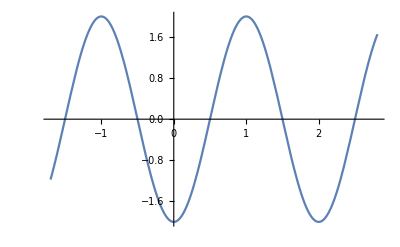

```mathematica
grf = Plot[f[x],{x,xt[[1]]-0.3,xt[[M]]+0.3}]
```

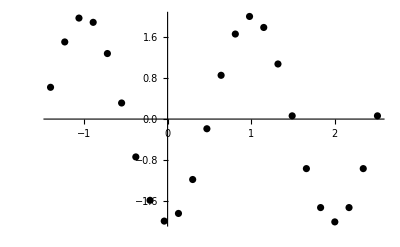

```mathematica
points = Table[{xt[[i]],yt[[i]]},{i,1,M}];
grp = ListPlot[points, PlotStyle->Black]
```

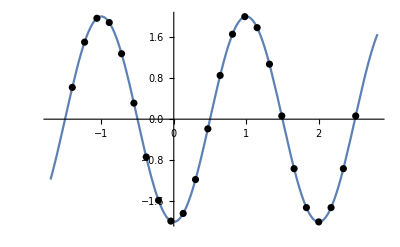

```mathematica
Show[grf,grp]
```

## Линейна регресия

### Попълване на таблицата

```mathematica
xt^2
```

{1.96,1.5129,1.1236,0.7921,0.5184,0.3025,0.1444,0.0441,0.0016,0.0169,0.09,0.2209,0.4096,0.6561,0.9604,1.3225,1.7424,2.2201,2.7556,3.3489,4.,4.7089,5.4756,6.3001}

```mathematica
yt*xt
```

{-0.865248,-1.84527,-2.08245,-1.67477,-0.917891,-0.172078,0.279775,0.331865,0.0793692,-0.238616,-0.352671,-0.0884618,0.544997,1.33987,1.95613,2.04932,1.41458,0.0936041,-1.59942,-3.15032,-4.,-3.73562,-2.25461,0.157682}

### Пресмятаме сумите

```mathematica
∑_(i=1)^M xt[[i]]
```

13.32

```mathematica
∑_(i=1)^M yt[[i]]
```

0.163324

```mathematica
∑_(i=1)^M xt[[i]]^2
```

40.6276

```mathematica
∑_(i=1)^M yt[[i]]*xt[[i]]
```

-14.7302

### Решаваме СЛАУ

```mathematica
A = ({{24, 13.32}, {13.32, 40.628}}); b = {0.163, -14.730};
LinearSolve[A,b]
```

{0.25428,-0.445924}

### Съставяме полинома

```mathematica
P1[x_]:= -0.446x+0.254
```

таен коз

```mathematica
Fit[points,{x,1},x]
```

0.254303-0.445942 x

#### Визуализация

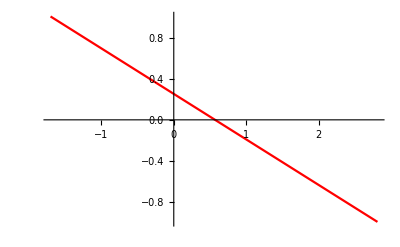

```mathematica
grP1 = Plot[P1[x],{x,xt[[1]]-0.3,xt[[M]]+0.3}, PlotStyle->Red]
```

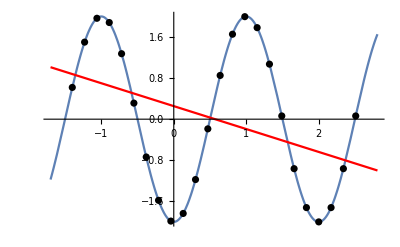

```mathematica
Show[grf,grp,grP1]
```

### Пресмятане на приближена стойност на функция (апроксимация)

#### Приближена стойност

```mathematica
P1[2.]
```

-0.638

#### Истинска стойност (за сравнение)

```mathematica
f[2.]
```

-2.

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^M (yt[[i]]-P1[xt[[i]]])^2)
```

6.36163

#### Истинска грешка

```mathematica
Abs[f[2.]-P1[2.]]
```

1.362

## Квадратична регресия

### Попълване на таблицата

```mathematica
xt^2
```

{1.96,1.5129,1.1236,0.7921,0.5184,0.3025,0.1444,0.0441,0.0016,0.0169,0.09,0.2209,0.4096,0.6561,0.9604,1.3225,1.7424,2.2201,2.7556,3.3489,4.,4.7089,5.4756,6.3001}

```mathematica
yt*xt
```

{-0.865248,-1.84527,-2.08245,-1.67477,-0.917891,-0.172078,0.279775,0.331865,0.0793692,-0.238616,-0.352671,-0.0884618,0.544997,1.33987,1.95613,2.04932,1.41458,0.0936041,-1.59942,-3.15032,-4.,-3.73562,-2.25461,0.157682}

```mathematica
xt^3
```

{-2.744,-1.86087,-1.19102,-0.704969,-0.373248,-0.166375,-0.054872,-0.009261,-0.000064,0.002197,0.027,0.103823,0.262144,0.531441,0.941192,1.52087,2.29997,3.30795,4.5743,6.12849,8.,10.2183,12.8129,15.8133}

```mathematica
xt^4
```

{3.8416,2.28887,1.26248,0.627422,0.268739,0.0915063,0.0208514,0.00194481,2.56×10^-6,0.00028561,0.0081,0.0487968,0.167772,0.430467,0.922368,1.74901,3.03596,4.92884,7.59333,11.2151,16.,22.1737,29.9822,39.6913}

```mathematica
yt*xt^2
```

{1.21135,2.26969,2.2074,1.49054,0.660881,0.0946429,-0.106314,-0.0696917,-0.00317477,-0.0310201,-0.105801,-0.0415771,0.348798,1.0853,1.91701,2.35671,1.86725,0.13947,-2.65504,-5.76508,-8.,-8.1063,-5.27578,0.395782}

### Пресмятаме сумите

```mathematica
∑_(i=1)^M xt[[i]]
```

13.32

```mathematica
∑_(i=1)^M yt[[i]]
```

0.163324

```mathematica
∑_(i=1)^M xt[[i]]^2
```

40.6276

```mathematica
∑_(i=1)^M yt[[i]]*xt[[i]]
```

-14.7302

```mathematica
∑_(i=1)^M xt[[i]]^3
```

59.4392

```mathematica
∑_(i=1)^M xt[[i]]^4
```

146.351

```mathematica
∑_(i=1)^M yt[[i]]*xt[[i]]^2
```

-14.115

### Решаваме СЛАУ

```mathematica
A = ({{24, 13.32, 40.628}, {13.32, 40.628, 59.439}, {40.628, 59.439, 146.351}}); b = {0.163, -14.730,-14.115};
LinearSolve[A,b]
```

{0.193735,-0.508334,0.0562265}

```mathematica
A = ({{M, ∑_(i=1)^M xt[[i]], ∑_(i=1)^M xt[[i]]^2}, {∑_(i=1)^M xt[[i]], ∑_(i=1)^M xt[[i]]^2, ∑_(i=1)^M xt[[i]]^3}, {∑_(i=1)^M xt[[i]]^2, ∑_(i=1)^M xt[[i]]^3, ∑_(i=1)^M xt[[i]]^4}}); b = {∑_(i=1)^M yt[[i]], ∑_(i=1)^M yt[[i]]*xt[[i]], ∑_(i=1)^M yt[[i]]*xt[[i]]^2};
a =LinearSolve[A,b]
```

{0.19375,-0.508363,0.0562356}

### Съставяме полинома

```mathematica
P2[x_]:=0.056226 x^2 -0.5083x+0.1937
```

```mathematica
P2[x_]:=a[[1]]+a[[2]]x+ a[[3]] x^2
```

```mathematica
P2[x]
```

0.19375-0.508363 x+0.0562356 x^2

таен коз

```mathematica
Fit[points,{x^2,x,1},x]
```

0.19375-0.508363 x+0.0562356 x^2

#### Визуализация

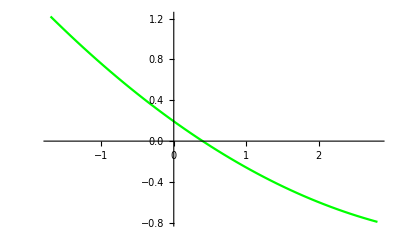

```mathematica
grP2 = Plot[P2[x],{x,xt[[1]]-0.3,xt[[M]]+0.3}, PlotStyle->Green]
```

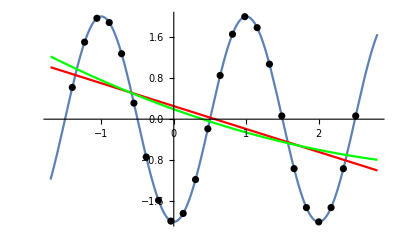

```mathematica
Show[grf,grp,grP1, grP2]
```

### Пресмятане на приближена стойност на функция (апроксимация)

#### Приближена стойност

```mathematica
P2[2.]
```

-0.597996

#### Истинска стойност (за сравнение)

```mathematica
f[2.]
```

-2.

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^M (yt[[i]]-P2[xt[[i]]])^2)
```

6.35252

#### Истинска грешка

```mathematica
Abs[f[2.]-P2[2.]]
```

1.402

## Кубична регресия

### Попълване на таблицата

```mathematica
xt^2
```

{1.96,1.5129,1.1236,0.7921,0.5184,0.3025,0.1444,0.0441,0.0016,0.0169,0.09,0.2209,0.4096,0.6561,0.9604,1.3225,1.7424,2.2201,2.7556,3.3489,4.,4.7089,5.4756,6.3001}

```mathematica
yt*xt
```

{-0.865248,-1.84527,-2.08245,-1.67477,-0.917891,-0.172078,0.279775,0.331865,0.0793692,-0.238616,-0.352671,-0.0884618,0.544997,1.33987,1.95613,2.04932,1.41458,0.0936041,-1.59942,-3.15032,-4.,-3.73562,-2.25461,0.157682}

```mathematica
xt^3
```

{-2.744,-1.86087,-1.19102,-0.704969,-0.373248,-0.166375,-0.054872,-0.009261,-0.000064,0.002197,0.027,0.103823,0.262144,0.531441,0.941192,1.52087,2.29997,3.30795,4.5743,6.12849,8.,10.2183,12.8129,15.8133}

```mathematica
xt^4
```

{3.8416,2.28887,1.26248,0.627422,0.268739,0.0915063,0.0208514,0.00194481,2.56×10^-6,0.00028561,0.0081,0.0487968,0.167772,0.430467,0.922368,1.74901,3.03596,4.92884,7.59333,11.2151,16.,22.1737,29.9822,39.6913}

```mathematica
yt*xt^2
```

{1.21135,2.26969,2.2074,1.49054,0.660881,0.0946429,-0.106314,-0.0696917,-0.00317477,-0.0310201,-0.105801,-0.0415771,0.348798,1.0853,1.91701,2.35671,1.86725,0.13947,-2.65504,-5.76508,-8.,-8.1063,-5.27578,0.395782}

добавяме необходимото

### Пресмятаме сумите

```mathematica
∑_(i=1)^M xt[[i]]
```

13.32

```mathematica
∑_(i=1)^M yt[[i]]
```

0.163324

```mathematica
∑_(i=1)^M xt[[i]]^2
```

40.6276

```mathematica
∑_(i=1)^M yt[[i]]*xt[[i]]
```

-14.7302

```mathematica
∑_(i=1)^M xt[[i]]^3
```

59.4392

```mathematica
∑_(i=1)^M xt[[i]]^4
```

146.351

```mathematica
∑_(i=1)^M yt[[i]]*xt[[i]]^2
```

-14.115

добавяме необходимото

### Решаваме СЛАУ

```mathematica
A = ({{M, ∑_(i=1)^M xt[[i]], ∑_(i=1)^M xt[[i]]^2, ∑_(i=1)^M xt[[i]]^3}, {∑_(i=1)^M xt[[i]], ∑_(i=1)^M xt[[i]]^2, ∑_(i=1)^M xt[[i]]^3, ∑_(i=1)^M xt[[i]]^4}, {∑_(i=1)^M xt[[i]]^2, ∑_(i=1)^M xt[[i]]^3, ∑_(i=1)^M xt[[i]]^4, ∑_(i=1)^M xt[[i]]^5}, {∑_(i=1)^M xt[[i]]^3, ∑_(i=1)^M xt[[i]]^4, ∑_(i=1)^M xt[[i]]^5, ∑_(i=1)^M xt[[i]]^6}}); b = {∑_(i=1)^M yt[[i]], ∑_(i=1)^M yt[[i]]*xt[[i]], ∑_(i=1)^M yt[[i]]*xt[[i]]^2, ∑_(i=1)^M yt[[i]]*xt[[i]]^3};
a =LinearSolve[A,b]
```

{-0.229343,0.0384226,0.63879,-0.349882}

### Съставяме полинома

```mathematica
P3[x_]:=a[[1]]+a[[2]]x+ a[[3]] x^2+ a[[4]] x^3
```

```mathematica
P3[x]
```

-0.229343+0.0384226 x+0.63879 x^2-0.349882 x^3

таен коз

```mathematica
Fit[points,{x^3,x^2,x,1},x]
```

-0.229343+0.0384226 x+0.63879 x^2-0.349882 x^3

#### Визуализация

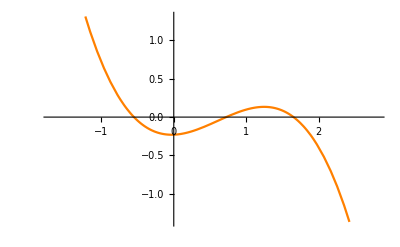

```mathematica
grP3 = Plot[P3[x],{x,xt[[1]]-0.3,xt[[M]]+0.3}, PlotStyle->Orange]
```

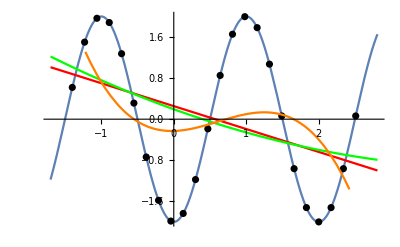

```mathematica
Show[grf,grp,grP1, grP2,grP3]
```

### Пресмятане на приближена стойност на функция (апроксимация)

#### Приближена стойност

```mathematica
P3[2.]
```

-0.396398

#### Истинска стойност (за сравнение)

```mathematica
f[2.]
```

-2.

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^M (yt[[i]]-P3[xt[[i]]])^2)
```

5.96919

#### Истинска грешка

```mathematica
Abs[f[2.]-P3[2.]]
```

1.6036